# 1-D universal estimator using CNN

## Generating data (without duplicating θ and logging the histogram)

Generates synthetic data for DNN :

Arguments:
	n: number of samples drawn for a given θ 
	M: number of different θ generated in the range [min_θ, max_θ]
	f: the distribution function for generating samples. f(θ, N) returns N observations using parameter θ
	range: range of the dist parameter θ
	bins: number of bins in the histograms generated from samples
Return:
	a table of associations(one row per sample): histogram->θ

```mathematica
GenerateData[M_, n_, f_, range_, bins_:-1]:=
	Module[{params, samples, nbins, MAXBINS},
		params=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
		(*generate M different random initparameters in the range [min_θ,max_θ]*) 
		samples=Table[f[params[[i]],n],{i,1,M}];
		(*generate M distributions, each distribution has n number/data*, now we have M*n data*)
		MAXBINS=5000;
		nbins=If[bins>0,bins,Min[MAXBINS, Ceiling[Max[samples]]+1](*Ceiling[Max[samples]]+2] if using zero padding*)];
		h[x_]:=HistogramList[x,{0,nbins,1}][[2]]; (*without using log10(x+1)*)
		Table[h@samples[[i]]->params[[i]], {i,1,M}]  
	
	]
```

## Example of generated data

```mathematica
(*f[å_,N_]:=RandomVariate[WaringYuleDistribution[å],N];
Print[GenerateData[5,10,f,{2,3}]//TableForm];*)
```

{8,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.28381
{5,3,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}→2.29096
{7,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.3542
{8,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.35051
{8,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1}→2.77108

## CNN (my own version)

Generate a DNN for predicting the parameter θ from the distribution histogram
The input size is the number of bins in the input histogram, the output is a scalar predicting the parameter used to generate the input sample.

```mathematica
CreateNet[bins_]:=( 
NetChain[{
ReshapeLayer[{1,bins}],  (*change the vector to 1d matrix for convolution*)
ConvolutionLayer[32,{4}], (*64 filters, kernel size 4*)
ElementwiseLayer[Ramp], (*relu activation*)
(*PoolingLayer[{2},"Function"->Max],*)  (*max pooling size 2*)
(*FlattenLayer[],*)
LinearLayer[{64}], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp], (*relu activation*)
LinearLayer[1]
},
"Input"->bins, 
"Output" -> "Scalar"]
)
```

## 1-D universal estimator using CNN

Given a distribution  dist(x|θ) and the range for the parameter θ,  
UniversalEstimator returns an Estimator function for predicting the parameter θ given an input sample S.

```mathematica
UniversalEstimator[dist_, range_]:=Module[{g, M, n, trainSet, bins, valSet ,net, trained, model, h},
(*define a sample generator*)
g[θ_,n_] := RandomVariate[dist[θ],n];

(*train a NN for predicting the parameter θ *)
(*generate learning samples in the the given parameter range*)
M = 10000; 
n = 2048;   (*number of observations in each sample*)
trainSet=GenerateData[M,n, g, range];
bins = Length@trainSet[[1]][[1]]; (*use the same number of bins for the validation set*)
valSet=GenerateData[M/2,n, g, range, bins];

(*Create and train the NN*)
net = NetInitialize@CreateNet[bins];

trained=NetTrain[
net,
trainSet,
All,
ValidationSet->valSet, 
TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->500|>, (*using loss criterion to prevent overfitting*)
Method->"ADAM" ,
BatchSize->256
 (*LearningRate->0.001 learning rate*)
 (*LossFunction->MeanSquaredLossLayer[] loss: mse*)
];

Print[trained];  (*print the training result*)

model = trained["TrainedNet"];

(*define a function for generating a histogram with nbins from an input sample )*)
h[x_]:=HistogramList[x,{0,bins,1}][[2]];

(*return an Estimator which is a fucntion map sample to a parameter*)
Function[{sample}, (
(*return a prediction of the parameter θ*)
model[h@sample]
)]
]
```

## Experiment of universal estimator with CNN

n: number of samples drawn for a given θ 
M: number of different θ generated in the range [min_θ, max_θ]
S: number of samples per θ

```mathematica
RunExperiment[dist_, range_]:= Module[{estimator, g, adjuster, params, n, samples, Θ, Θhat, e, TestSet, M, initΘ, expansion,S},
(*generate an Estimator for dist*)
estimator = UniversalEstimator[dist, range];
(*define the size of the test set*)
M = 20;
S = 5；
n = 2048;

initΘ=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
(*generate M different random initΘ in the range [min_θ,max_θ]*)
expansion[j_]:=Table[initΘ[[j]],S]; 
(*define an expansion function for duplicating the initΘ*)
Θ=Flatten[Table[expansion[w],{w,1,M}]];
(*increase the number of each different parameters to S, now we have M*S Θ *)		
g[θ_,a_] := RandomVariate[dist[θ],a];
(*create M*S test samples*)
samples = Table[g[Θ[[i]], n], {i,1,M*S,1 }];

(*predict the parameter for each sample*)
Θhat = Table[estimator[samples[[i]]], {i,1,M*S,1 }];

(*evaluate prediction errors*)

e = Table[Abs[Θ[[i]] - Θhat[[i]]], {i,1,M*S,1 }];

Print["θ: ",Θ];
Print["θ̂: ",Θhat];
Print["abs(θ-θ̂): ",e];
Print["RMSE:",RootMeanSquare[e]];

(*return true parameters and predicted errors*)
{Θ, e}
]
```

## Run the experiment for the different distributions

### Yule-Simon distribution

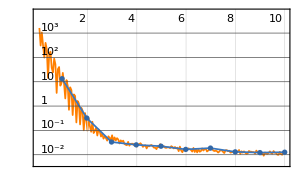
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:400  rounds:10  time:2.8min  examples/s:614
data | ,,  training examples:10000  validation examples:5000  processed examples:102400  skipped examples:0
method | ,,  ADAMoptimizer  batch size256CPU
round | ,,  loss:1.15×10^-2
validation | ,,  loss:1.27×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {2.57276,2.57276,2.57276,2.57276,2.57276,2.39278,2.39278,2.39278,2.39278,2.39278,2.65162,2.65162,2.65162,2.65162,2.65162,2.52159,2.52159,2.52159,2.52159,2.52159,2.41471,2.41471,2.41471,2.41471,2.41471,2.73445,2.73445,2.73445,2.73445,2.73445,2.40334,2.40334,2.40334,2.40334,2.40334,2.32387,2.32387,2.32387,2.32387,2.32387,2.4218,2.4218,2.4218,2.4218,2.4218,2.38566,2.38566,2.38566,2.38566,2.38566,2.29306,2.29306,2.29306,2.29306,2.29306,2.17449,2.17449,2.17449,2.17449,2.17449,2.13776,2.13776,2.13776,2.13776,2.13776,2.93004,2.93004,2.93004,2.93004,2.93004,2.58367,2.58367,2.58367,2.58367,2.58367,2.87862,2.87862,2.87862,2.87862,2.87862,2.4157,2.4157,2.4157,2.4157,2.4157,2.84688,2.84688,2.84688,2.84688,2.84688,2.23458,2.23458,2.23458,2.23458,2.23458,2.53745,2.53745,2.53745,2.53745,2.53745}

θ̂: {2.63635,2.3979,2.60498,2.54572,2.66545,2.53989,2.50662,2.28064,2.40801,2.4871,2.80982,2.67531,2.70907,2.68784,2.58605,2.51014,2.42248,2.48494,2.66536,2.58467,2.38327,2.44882,2.58295,2.39634,2.50753,2.61097,2.76543,2.86798,2.58761,2.78893,2.41245,2.31662,2.37262,2.45631,2.63128,2.35211,2.39169,2.30531,2.42534,2.36732,2.25723,2.4472,2.42805,2.4566,2.47263,2.35527,2.48137,2.29273,2.21623,2.4144,2.15129,2.35296,2.22327,2.3578,2.29203,2.15517,2.13141,1.9558,2.19741,2.28967,2.28397,2.41229,2.0611,2.11832,2.0939,2.87773,2.83678,2.86002,2.95595,2.66062,2.50904,2.32799,2.56687,2.66123,2.5417,2.89709,2.64088,2.70061,2.76607,2.83331,2.35871,2.68092,2.31875,2.53088,2.43528,2.78141,2.81412,2.8317,2.86457,2.61633,2.41041,2.24175,2.06662,2.23463,2.03803,2.56598,2.58347,2.55529,2.67538,2.51849}

abs(θ-θ̂): {0.0635858,0.174861,0.0322149,0.0270436,0.0926862,0.147112,0.113841,0.112136,0.0152314,0.0943244,0.158193,0.0236822,0.0574437,0.0362182,0.0655713,0.0114445,0.0991048,0.0366484,0.14377,0.0630821,0.031435,0.0341146,0.168245,0.0183665,0.0928202,0.12348,0.0309853,0.133532,0.146837,0.0544814,0.00910951,0.0867197,0.0307212,0.0529695,0.227932,0.0282401,0.0678187,0.0185629,0.101472,0.0434528,0.164568,0.0254,0.00625503,0.0347954,0.050835,0.030389,0.0957137,0.0929295,0.169426,0.0287414,0.141769,0.0599034,0.0697834,0.0647378,0.00102969,0.0193288,0.043083,0.21869,0.0229173,0.115175,0.146212,0.27453,0.076659,0.0194424,0.0438598,0.05231,0.0932613,0.0700169,0.0259113,0.26942,0.0746281,0.255681,0.0167939,0.07756,0.0419731,0.0184742,0.237736,0.178008,0.112541,0.0453035,0.0569907,0.265219,0.0969556,0.115175,0.019577,0.0654697,0.032757,0.0151807,0.0176924,0.230553,0.175829,0.00716812,0.167961,0.0000549051,0.196551,0.0285325,0.0460169,0.017838,0.137929,0.018961}

RMSE:0.10864

```mathematica
{Θ, e} = RunExperiment[WaringYuleDistribution, {2,3}];
```

### Poisson distribution

### Geometric distribution